## Husimis

## Definiciones

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\INVESTIGACION\2025\PAPER II Scaling fluctuations\LMG

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
(*Operadores*)
Clear[Sz,SM,Sm,Sx,a2,F];

Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
(*Estados coherentes*)
Clear[a2];
a2[J_,Q_,P_]:=Module[{z=-1+(Q^2+P^2)/2,ϕ=ArcTan[-(P/Q)]},
N[Table[1/((1+Tan[ArcCos[-z]/2]^2)^J)Sqrt[Binomial[2J,J+(m-J)]] Tan[ArcCos[-z]/2]^(J+(m-J))Exp[-I(J+(m-J))ϕ],{m,0,2J}],20]
];

Clear[H];
F[J_,α_,k_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])+(-I*α)(Sz[J])]];
H[J_,α_,k_]:=N[(k/(2J))(Sx[J].Sx[J])+(α)(Sz[J])];

Clear[Tq];
Tq[q_]:=Module[{a,b,points=allpointsx[[q]]},
{a,b}=CoefficientList[Fit[points,{1,x},x],x];
{qlist[[q]],-b}
];

Clear[IPR];
IPR[J_,q_,ini_]:=Module[{a},
Log[Sum[Abs[Conjugate[eigen[[j]]].ini]^(2q),{j,1,2J+1}]]
];

Clear[Dq];
Dq[Q_,P_,q_,J_]:=Module[{floq=eigen,cohe=Quiet[a2[J,Q,P]],a},
a=(1/(1-q))Log[Sum[Abs[Conjugate[floq[[i]]].cohe]^(2q),{i,1,2J+1}]]/Log[2J+1]
];
```

## Husimis

```mathematica
Clear[a2];
a2[J_,Q_,P_]:=a2[J,Q,P]=Module[{z=-1+(Q^2+P^2)/2,ϕ=ArcTan[-(P/Q)]},
N[Table[1/((1+Tan[ArcCos[-z]/2]^2)^J)Sqrt[Binomial[2J,J+(m-J)]] Tan[ArcCos[-z]/2]^(J+(m-J))Exp[-I(J+(m-J))ϕ],{m,0,2J}],20]
];
```

```mathematica
Clear[husi];
husi[J_,Q_,P_,ini_]:=Module[{cohe=a2[J,Q,P]},
Abs[Conjugate[ini].cohe]^2
];
```

```mathematica
dq=0.05;
region=Flatten[ParallelTable[If[Sqrt[i^2+j^2]<2,{i,j},{0,0}],{i,-2.0+dq,2.0-dq,dq},{j,-2.0+dq,2.0-dq,dq}],1];
region=DeleteCases[region,_{0,0}];
region=Sort[AppendTo[region,{0,0}]];
region//Length
```

5014

```mathematica
k=-2;
α=0.84;
```

```mathematica
Clear[J,mat,eigenvec];
J=1000;
mat=H[N[J],α,k];
{val,eigenvec}=Transpose[Sort[Transpose[Eigensystem[mat]]]];
```

```mathematica
husimis={};
Do[
data=ParallelTable[{region[[i,1]],region[[i,2]],Quiet[husi[J,region[[i,1]],region[[i,2]],eigenvec[[j]]]]},{i,Length[region]}];
AppendTo[husimis,data];
,{j,Range[89,450]}];

Do[
husimiplot=ListDensityPlot[husimis[[j]],PlotRange->All,ColorFunction->"BlueGreenYellow",PlotTheme->"Detailed"];
Export["Husimi_J_"<>ToString[J]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[dq]<>"_eigenvec_"<>ToString[j]<>".jpg",husimiplot,ImageSize->800];
,{j,Length[eigenvec]}];
```

$Aborted

$Aborted

```mathematica
Do[
husimiplot=ListDensityPlot[husimis[[j]],PlotRange->All,ColorFunction->"BlueGreenYellow",PlotTheme->"Detailed"];
Export["Husimi_J_"<>ToString[J]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[dq]<>"_eigenvec_"<>ToString[j]<>".jpg",husimiplot,ImageSize->800];
,{j,Length[husimis]}];
```

## Espectro

```mathematica
k=30.0;
α=0.84;
```

```mathematica
Clear[J,mat,eigenvec];
J=100;
mat=H[N[J],α,k];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[mat]]]];
```

```mathematica
jz=ParallelTable[Chop[Transpose[Conjugate[eigenvec[[i]]]].Sz[J].eigenvec[[i]]],{i,1,2J+1}];
sortedjz=Sort[jz];
index=Table[Flatten[Position[jz,sortedjz[[i]]]],{i,1,2J+1}];
sortedeigenvec=Table[eigenvec[[i[[1]]]],{i,index}];
```

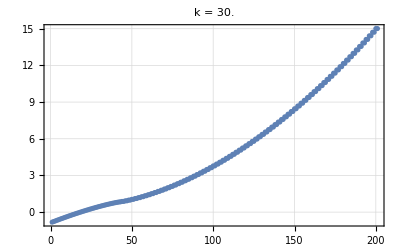

```mathematica
ListPlot[eigenval/J,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["k = "<>ToString[k],23,Black]]
```

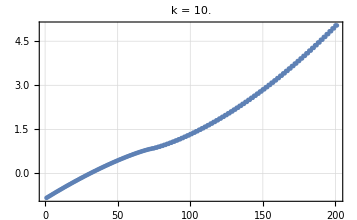

```mathematica
ListPlot[eigenval/J,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["k = "<>ToString[k],23,Black]]
```

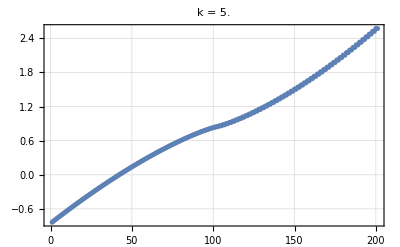

```mathematica
ListPlot[eigenval/J,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["k = "<>ToString[k],23,Black]]
```

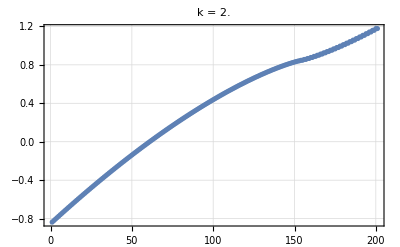

```mathematica
ListPlot[eigenval/J,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["k = "<>ToString[k],23,Black]]
```

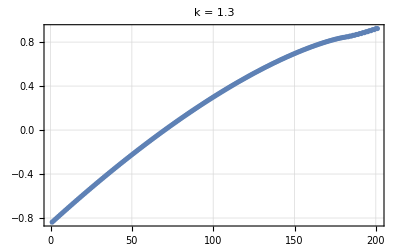

```mathematica
ListPlot[eigenval/J,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["k = "<>ToString[k],23,Black]]
```

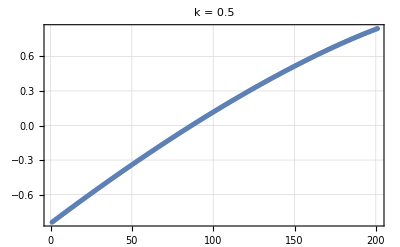

```mathematica
ListPlot[eigenval/J,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["k = "<>ToString[k],23,Black]]
```

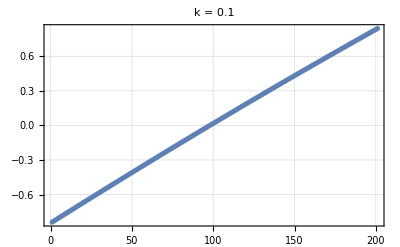

```mathematica
ListPlot[eigenval/J,PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["k = "<>ToString[k],23,Black]]
```

## LMG

```mathematica
Clear[h2M,h2m];
h2M[α_,k_,Q_,P_]:=α((1/2)(Q^2+P^2)-1)+(k*Q^2)(1-(1/4)(Q^2+P^2));
```

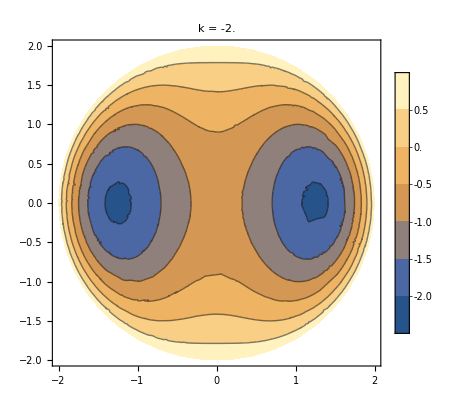
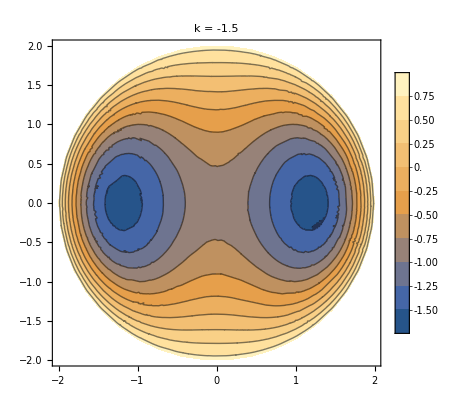
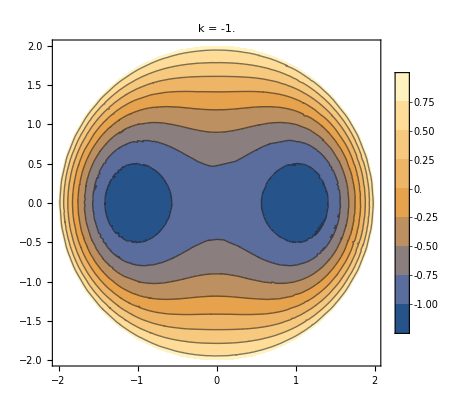
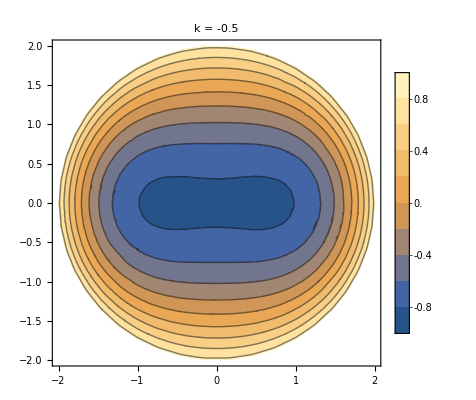
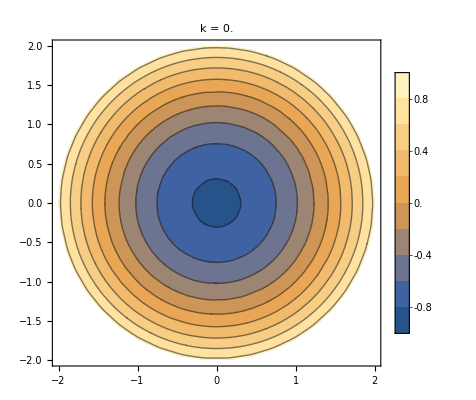
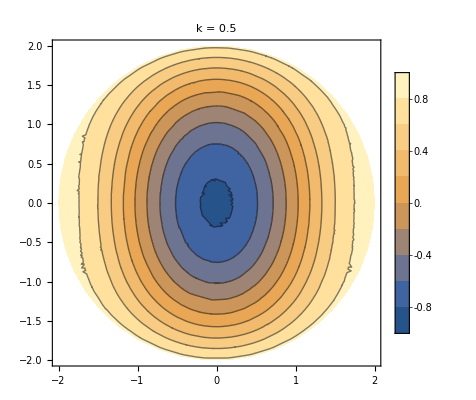
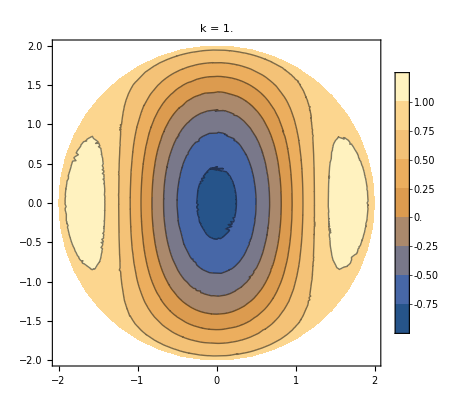

```mathematica
Clear[α,k];
α=0.84;
Table[ContourPlot[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["k = "<>ToString[k],23,Black]],{k,-2,1,0.5}]
```

## Coherentes en H

### k = -2

```mathematica
k=-2;
α=0.84;
```

```mathematica
Plot3D[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["k = "<>ToString[k],23,Black]]
```

-Graphics3D-

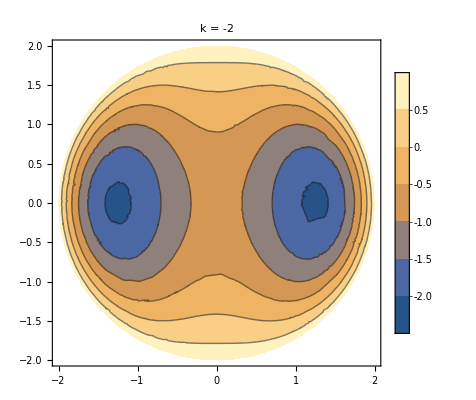

```mathematica
ContourPlot[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["k = "<>ToString[k],23,Black]]
```

```mathematica
Clear[J,mat,eigenvec];
J=100;
mat=H[N[J],α,k];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[mat]]]];
```

```mathematica
jz=ParallelTable[Chop[Transpose[Conjugate[eigenvec[[i]]]].Sz[J].eigenvec[[i]]],{i,1,2J+1}];
sortedjz=Sort[jz];
index=Table[Flatten[Position[jz,sortedjz[[i]]]],{i,1,2J+1}];
sortedeigenvec=Table[eigenvec[[i[[1]]]],{i,index}];
sortedeigenval=Table[eigenval[[i[[1]]]],{i,index}];
```

```mathematica
ListPlot[{eigenval/J,sortedeigenval/J},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", k = "<>ToString[k],23,Black],PlotLegends->Automatic]
```

```mathematica
Qs=Table[{Rationalize[i],1/10000},{i,1/10000,1.7,0.01}];
Length[Qs]
```

170

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,Qs}];
```

```mathematica
ListPlot[Quiet[Abs[cohes]^2],PlotRange->All,Filling->Axis,PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}]]
```

```mathematica
plotcohes=Table[ListPlot[Quiet[Abs[cohes[[i]]]^2],PlotRange->All,Filling->Axis,PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}][[i]]],{i,Length[cohes]}];
```

```mathematica
proba1=ParallelTable[Quiet[Abs[Conjugate[eigenvec[[i]].cohes[[j]]]]^2],{j,Length[cohes]},{i,Length[eigenvec]}];
proba2=ParallelTable[Transpose[{eigenval/J,proba1[[i]]}],{i,Length[proba1]}];
```

```mathematica
ListPlot[proba2,PlotRange->{{-1.2,-0.96},All},Filling->Axis,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["J = "<>ToString[J]<>", k = "<>ToString[k],25,Black],PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}]]
```

-Graphics-

```mathematica
probas1=Table[ListPlot[proba1[[i]],PlotRange->All,Filling->Axis,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", k = "<>ToString[k]<>", (Q,P) = "<>ToString[N[Qs[[i]]]],25,Black],PlotStyle->Brown],{i,Length[proba1]}];
```

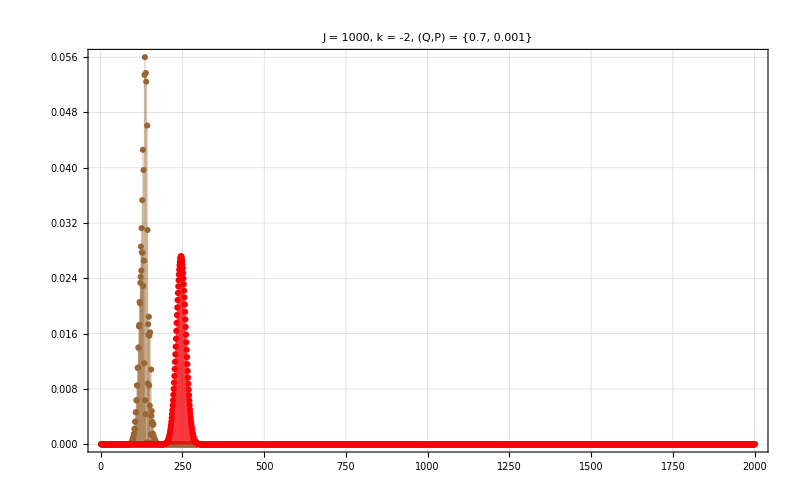
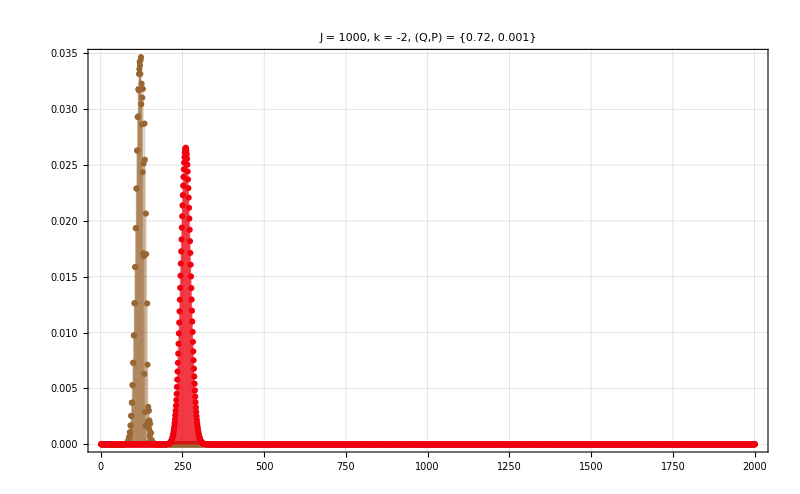
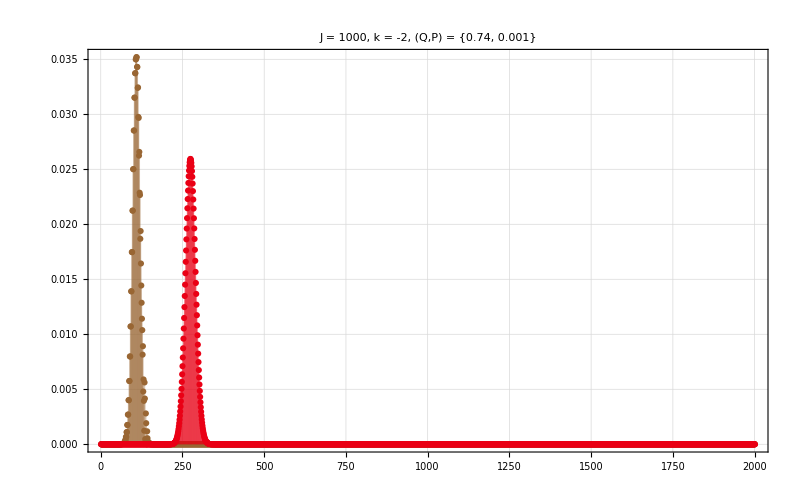
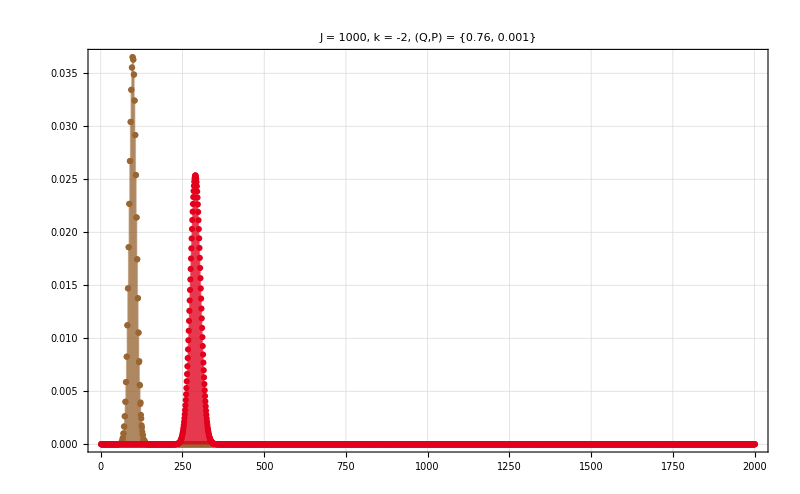
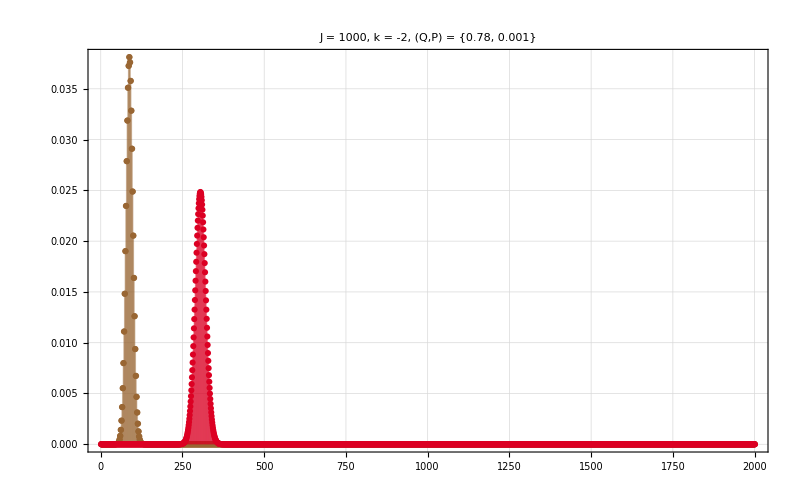
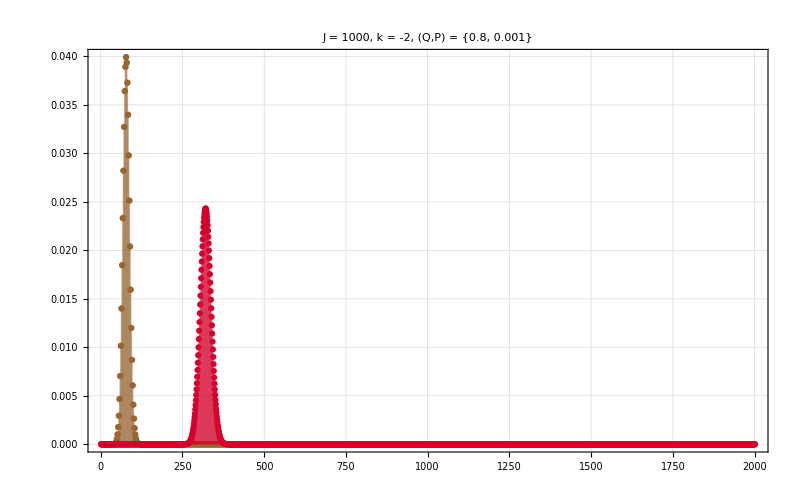
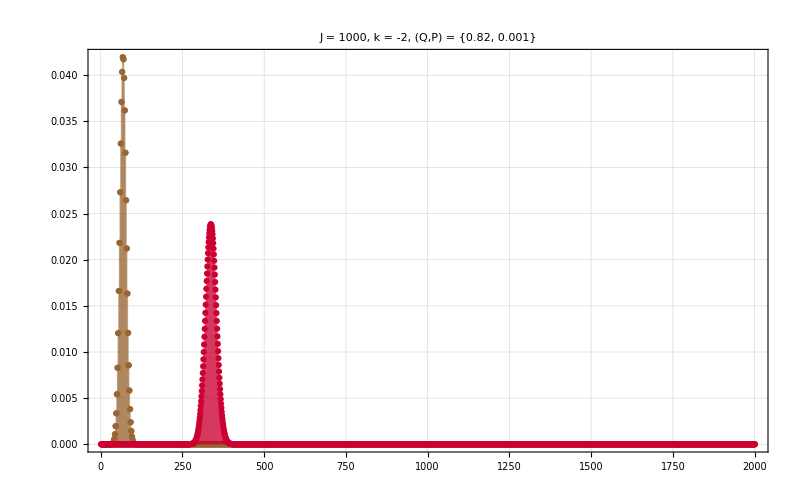
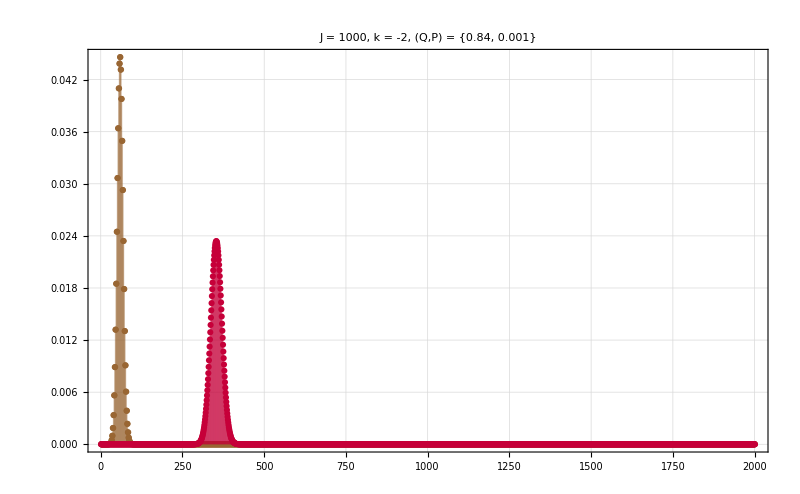

```mathematica
Table[Show[{probas1[[i]],plotcohes[[i]]},PlotRange->All,ImageSize->800],{i,Length[cohes]}]
```

### k = -1.5

```mathematica
k=-1.5;
α=0.84;
```

```mathematica
ContourPlot[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["k = "<>ToString[k],23,Black]]
```

-Graphics-

```mathematica
Clear[J,mat,eigenvec];
J=500;
mat=H[N[J],α,k];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[mat]]]];
```

```mathematica
jz=ParallelTable[Chop[Transpose[Conjugate[eigenvec[[i]]]].Sz[J].eigenvec[[i]]],{i,1,2J+1}];
sortedjz=Sort[jz];
index=Table[Flatten[Position[jz,sortedjz[[i]]]],{i,1,2J+1}];
sortedeigenvec=Table[eigenvec[[i[[1]]]],{i,index}];
sortedeigenval=Table[eigenval[[i[[1]]]],{i,index}];
```

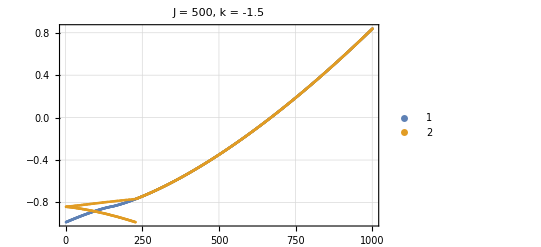

```mathematica
ListPlot[{eigenval/J,sortedeigenval/J},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", k = "<>ToString[k],23,Black],PlotLegends->Automatic]
```

```mathematica
Qs=Table[{Rationalize[i],1/100},{i,0.1,1.9,0.047}];
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,Qs}];
```

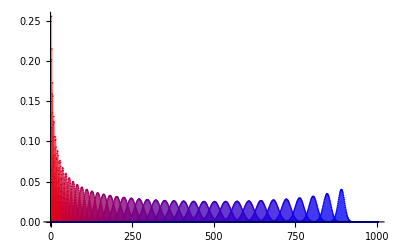

```mathematica
ListPlot[Quiet[Abs[cohes]^2],PlotRange->All,Filling->Axis,PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}]]
```

```mathematica
plotcohes=Table[ListPlot[Quiet[Abs[cohes[[i]]]^2],PlotRange->All,Filling->Axis,PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}][[i]]],{i,Length[cohes]}];
```

```mathematica
proba1=ParallelTable[Quiet[Abs[Conjugate[eigenvec[[i]].cohes[[j]]]]^2],{j,Length[cohes]},{i,Length[eigenvec]}];
proba2=Table[Transpose[{eigenval/J,proba1[[i]]}],{i,Length[proba1]}];
```

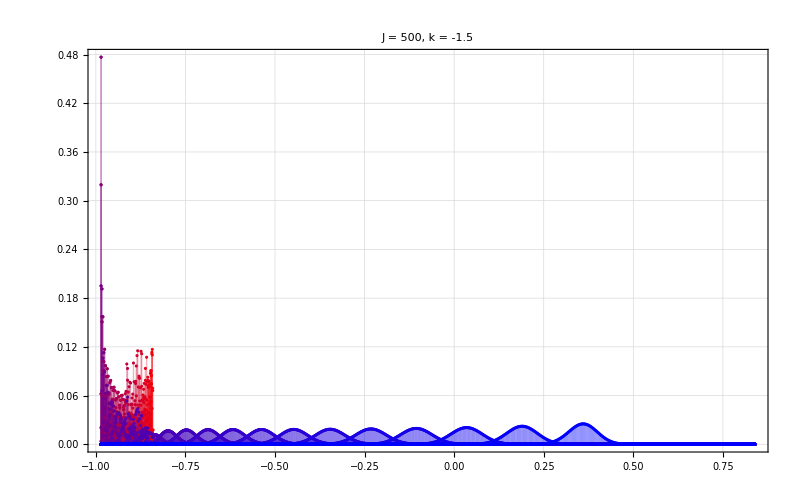

```mathematica
ListPlot[proba2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["J = "<>ToString[J]<>", k = "<>ToString[k],25,Black],PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}]]
```

```mathematica
probas1=Table[ListPlot[proba1[[i]],PlotRange->All,Filling->Axis,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", k = "<>ToString[k]<>", (Q,P) = "<>ToString[N[Qs[[i]]]],25,Black],PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}][[i]]],{i,Length[proba1]}];
```

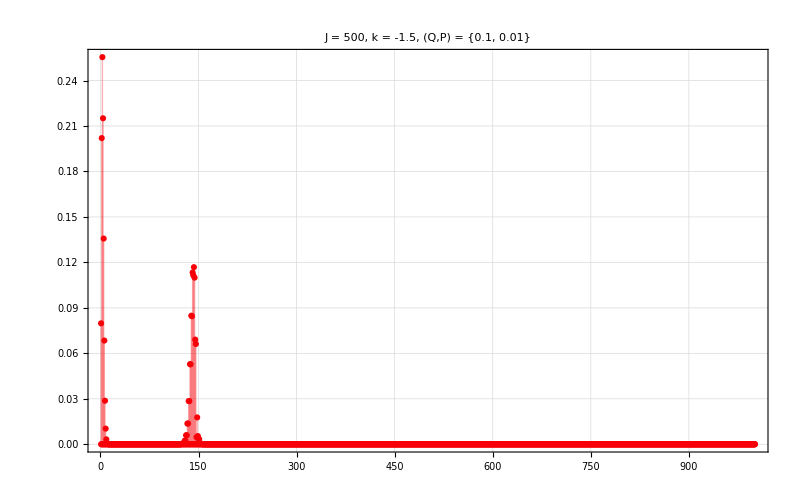
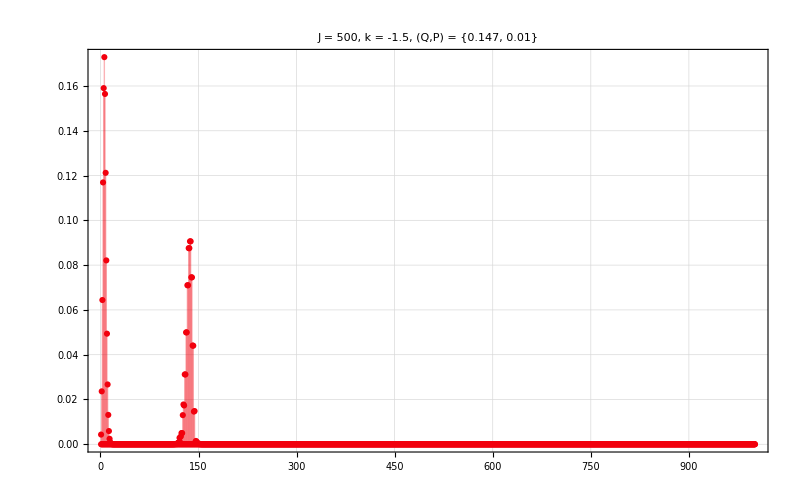
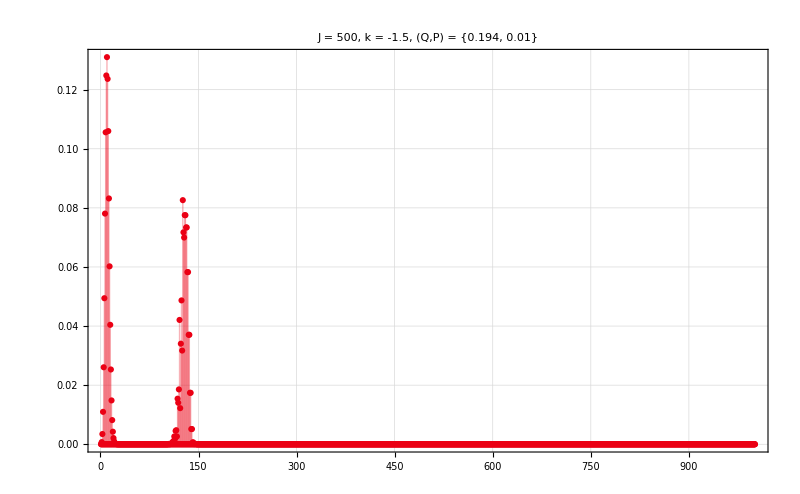
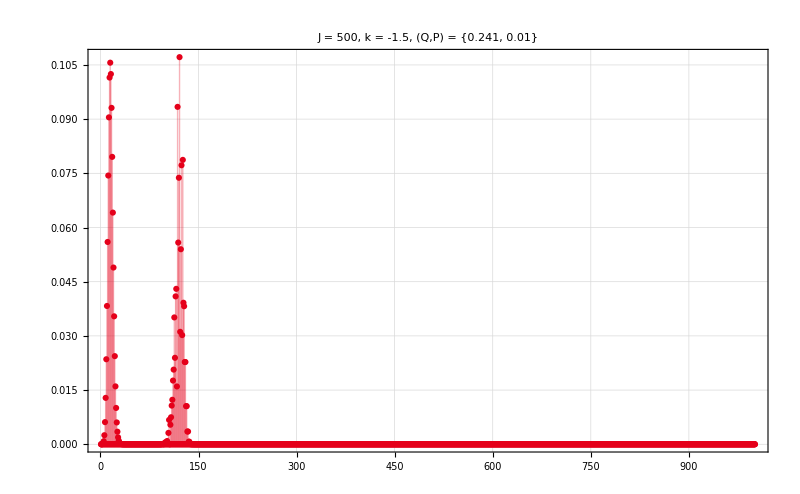
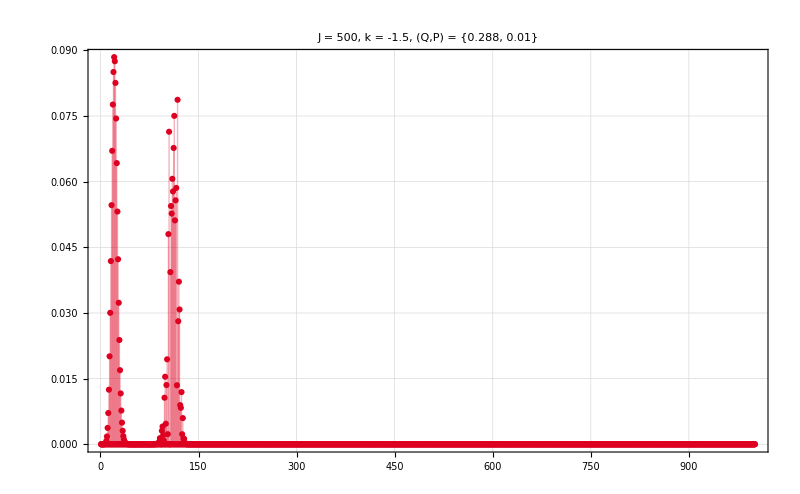
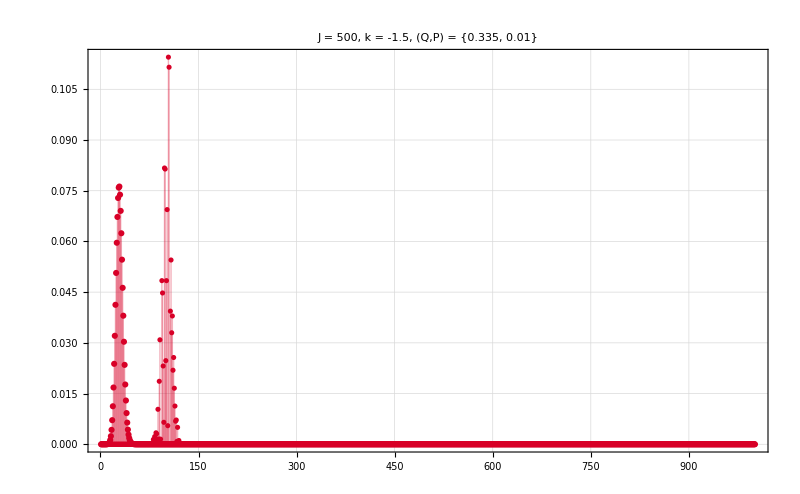
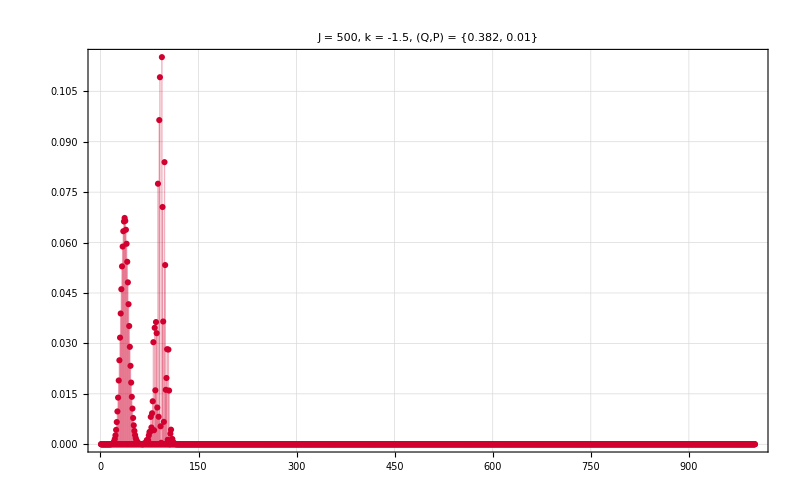
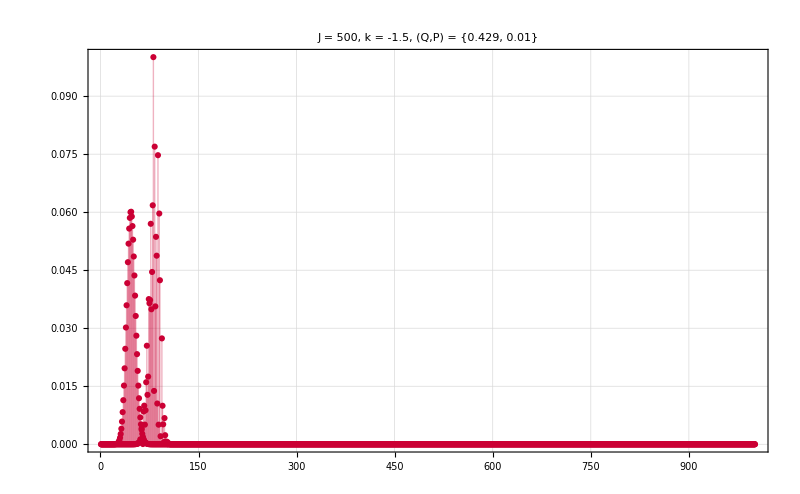
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{probas1[[i]],plotcohes[[i]]},PlotRange->All,ImageSize->800],{i,Length[cohes]}]
```

### k = -0.5

```mathematica
k=-0.5;
α=0.84;
```

```mathematica
ContourPlot[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["k = "<>ToString[k],23,Black]]
```

-Graphics-

```mathematica
Clear[J,mat,eigenvec];
J=500;
mat=H[N[J],α,k];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[mat]]]];
```

```mathematica
jz=ParallelTable[Chop[Transpose[Conjugate[eigenvec[[i]]]].Sz[J].eigenvec[[i]]],{i,1,2J+1}];
sortedjz=Sort[jz];
index=Table[Flatten[Position[jz,sortedjz[[i]]]],{i,1,2J+1}];
sortedeigenvec=Table[eigenvec[[i[[1]]]],{i,index}];
sortedeigenval=Table[eigenval[[i[[1]]]],{i,index}];
```

```mathematica
ListPlot[{eigenval/J,sortedeigenval/J},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", k = "<>ToString[k],23,Black],PlotLegends->Automatic]
```

-Graphics-

```mathematica
Qs=Table[{Rationalize[i],1/100},{i,0.1,1.9,0.047}];
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,Qs}];
```

```mathematica
ListPlot[Quiet[Abs[cohes]^2],PlotRange->All,Filling->Axis,PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}]]
```

-Graphics-

```mathematica
plotcohes=Table[ListPlot[Quiet[Abs[cohes[[i]]]^2],PlotRange->All,Filling->Axis,PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}][[i]]],{i,Length[cohes]}];
```

```mathematica
proba1=ParallelTable[Quiet[Abs[Conjugate[eigenvec[[i]].cohes[[j]]]]^2],{j,Length[cohes]},{i,Length[eigenvec]}];
proba2=Table[Transpose[{eigenval/J,proba1[[i]]}],{i,Length[proba1]}];
```

```mathematica
ListPlot[proba2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["J = "<>ToString[J]<>", k = "<>ToString[k],25,Black],PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}]]
```

-Graphics-

```mathematica
probas1=Table[ListPlot[proba1[[i]],PlotRange->All,Filling->Axis,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", k = "<>ToString[k]<>", (Q,P) = "<>ToString[N[Qs[[i]]]],25,Black],PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}][[i]]],{i,Length[proba1]}];
```

```mathematica
Table[Show[{probas1[[i]],plotcohes[[i]]},PlotRange->All,ImageSize->800],{i,Length[cohes]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### k = +1

```mathematica
k=1;
α=0.84;
```

```mathematica
ContourPlot[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["k = "<>ToString[k],23,Black]]
```

-Graphics-

```mathematica
Clear[J,mat,eigenvec];
J=500;
mat=H[N[J],α,k];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[mat]]]];
```

```mathematica
jz=ParallelTable[Chop[Transpose[Conjugate[eigenvec[[i]]]].Sz[J].eigenvec[[i]]],{i,1,2J+1}];
sortedjz=Sort[jz];
index=Table[Flatten[Position[jz,sortedjz[[i]]]],{i,1,2J+1}];
sortedeigenvec=Table[eigenvec[[i[[1]]]],{i,index}];
sortedeigenval=Table[eigenval[[i[[1]]]],{i,index}];
```

```mathematica
ListPlot[{eigenval/J,sortedeigenval/J},PlotRange->All,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", k = "<>ToString[k],23,Black],PlotLegends->Automatic]
```

-Graphics-

```mathematica
Qs=Table[{Rationalize[i],1/100},{i,-1.9,1.9,0.047}];
Length[Qs]
```

81

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,Qs}];
```

```mathematica
plotcohes=Table[ListPlot[Quiet[Abs[cohes[[i]]]^2],PlotRange->All,Filling->Axis,PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}][[i]]],{i,Length[cohes]}];
ListPlot[Quiet[Abs[cohes]^2],PlotRange->All,Filling->Axis,PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}]]
```

-Graphics-

```mathematica
proba1=ParallelTable[Quiet[Abs[Conjugate[eigenvec[[i]].cohes[[j]]]]^2],{j,Length[cohes]},{i,Length[eigenvec]}];
proba2=Table[Transpose[{eigenval/J,proba1[[i]]}],{i,Length[proba1]}];
```

```mathematica
ListPlot[proba2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["J = "<>ToString[J]<>", k = "<>ToString[k],25,Black],PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}]]
```

-Graphics-

```mathematica
probas1=Table[ListPlot[proba1[[i]],PlotRange->All,Filling->Axis,PlotTheme->"Detailed",PlotLabel->Style["J = "<>ToString[J]<>", k = "<>ToString[k]<>", (Q,P) = "<>ToString[N[Qs[[i]]]],25,Black],PlotStyle->Brown],{i,Length[proba1]}];
```

```mathematica
Table[Show[{probas1[[i]],plotcohes[[i]]},PlotRange->All,ImageSize->800],{i,Length[cohes]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Un estado coherente en base H

```mathematica
k=-2;
α=0.84;
```

```mathematica
ContourPlot[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["k = "<>ToString[k],23,Black]]
```

-Graphics-

```mathematica
Qs={-Rationalize[1.4],1/1000};
```

```mathematica
Clear[J,mat,eigenvec];
J=1000;
mat=H[N[J],α,k];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[mat]]]];
```

```mathematica
cohe=Quiet[a2[J,Qs[[1]],Qs[[2]]]];
```

```mathematica
plotcohe=ListPlot[Quiet[Abs[cohe]^2],PlotRange->All,Filling->Axis,PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}]]
```

-Graphics-

```mathematica
proba1=ParallelTable[Quiet[Abs[Conjugate[eigenvec[[i]].cohe]]^2],{i,Length[eigenvec]}];
proba2=Transpose[{eigenval/J,proba1}];
```

```mathematica
ListPlot[proba2,PlotRange->{{-1.1,-0.9},All},Filling->Axis,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["J = "<>ToString[J]<>", k = "<>ToString[k],25,Black],PlotStyle->Brown]
```

-Graphics-

```mathematica
Show[{plotcohe,probas},ImageSize->800]
```

-Graphics-

```mathematica
Clear[J,mat,eigenvec];
J=100;
mat=H[N[J],α,k];
```

```mathematica
Qs=Table[{Rationalize[i],0},{i,0.010,2-0.010,0.010}];
Qs//Length
```

199

```mathematica
region=Table[{Rationalize[i],1/10000},{i,-1.9,1.9,0.01}];
```

```mathematica
data1=ParallelTable[{i[[1]],Chop[Quiet[ConjugateTranspose[a2[J,i[[1]],i[[2]]]].mat.a2[J,i[[1]],i[[2]]]]]/J},{i,region}];
```

```mathematica
data2=ParallelTable[{{i[[1]],Chop[Quiet[ConjugateTranspose[a2[J,i[[1]],i[[2]]]].mat.a2[J,i[[1]],i[[2]]]]]/J}},{i,Qs}];
```

```mathematica
plot1=ListPlot[data1,PlotStyle->{Directive[Gray,Opacity[0.25]],Directive[Black]},PlotRange->All,ImageSize->600,PlotLabel->Style["J = "<>ToString[J],Black,23],AxesOrigin->{0,0},PlotTheme->"Detailed",Frame->True,Axes->True];
plot2=ListPlot[data2,PlotRange->All,ImageSize->600,PlotLabel->Style["J = "<>ToString[J],Black,23],PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}],AxesOrigin->{0,0},PlotTheme->"Detailed"];
Show[plot1,plot2]
```

-Graphics-

```mathematica
Clear[a,b];
a=12;
b=32;
plot1=ListPlot[data1,PlotStyle->{Directive[Gray,Opacity[0.25]],Directive[Black]},PlotRange->All,ImageSize->600,PlotLabel->Style["J = "<>ToString[J],Black,23]];
plot2a=ListPlot[data2[[a;;b]],PlotRange->All,ImageSize->600,PlotLabel->Style["J = "<>ToString[J],Black,23],PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}][[a;;b]],AxesOrigin->{0,0},PlotTheme->"Detailed",Frame->True,Axes->True];
Clear[a,b];
a=32;
b=52;
plot2b=ListPlot[data2[[a;;b]],PlotRange->All,ImageSize->600,PlotLabel->Style["J = "<>ToString[J],Black,23],PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}][[a;;b]],AxesOrigin->{0,0},PlotTheme->"Detailed",Frame->True,Axes->True];
Clear[a,b];
a=52;
b=75;
plot2c=ListPlot[data2[[a;;b]],PlotRange->All,ImageSize->600,PlotLabel->Style["J = "<>ToString[J],Black,23],PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}][[a;;b]],AxesOrigin->{0,0},PlotTheme->"Detailed",Frame->True,Axes->True];

Clear[a,b];
a=132;
b=153;
plot2d=ListPlot[data2[[a;;b]],PlotRange->All,ImageSize->600,PlotLabel->Style["J = "<>ToString[J],Black,23],PlotStyle->Table[RGBColor[1-i/Length[Qs],0,i/Length[Qs]],{i,Length[Qs]}][[a;;b]],AxesOrigin->{0,0},PlotTheme->"Detailed",Frame->True,Axes->True];
```

```mathematica
Clear[a,b];
a=1;
b=11;
plot4=ListPlot[data2[[a;;b]],PlotRange->All,ImageSize->600,PlotLabel->Style["J = "<>ToString[J],Black,23],PlotStyle->Green,AxesOrigin->{0,0},PlotTheme->"Detailed",Frame->True,Axes->True];
Clear[a,b];
a=76;
b=100;
plot5=ListPlot[data2[[a;;b]],PlotRange->All,ImageSize->600,PlotLabel->Style["J = "<>ToString[J],Black,23],PlotStyle->Green,AxesOrigin->{0,0},PlotTheme->"Detailed",Frame->True,Axes->True];
Clear[a,b];
a=101;
b=120;
plot6=ListPlot[data2[[a;;b]],PlotRange->All,ImageSize->600,PlotLabel->Style["J = "<>ToString[J],Black,23],PlotStyle->Green,AxesOrigin->{0,0},PlotTheme->"Detailed",Frame->True,Axes->True];
Clear[a,b];
a=121;
b=131;
plot7=ListPlot[data2[[a;;b]],PlotRange->All,ImageSize->600,PlotLabel->Style["J = "<>ToString[J],Black,23],PlotStyle->Green,AxesOrigin->{0,0},PlotTheme->"Detailed",Frame->True,Axes->True];
Clear[a,b];
a=154;
b=199;
plot8=ListPlot[data2[[a;;b]],PlotRange->All,ImageSize->600,PlotLabel->Style["J = "<>ToString[J],Black,23],PlotStyle->Green,AxesOrigin->{0,0},PlotTheme->"Detailed",Frame->True,Axes->True];
```

```mathematica
Show[plot2a,plot2b,plot2c,plot2d,plot4,plot5,plot6,plot7,plot8,plot1,PlotRange->{{0,2},{-0.4,-1.2}},AxesOrigin->{0,0},PlotTheme->"Detailed",Frame->True,Axes->True]
```

-Graphics-